```mathematica
MakeEdges[l_]:=Table[l[[k]]<->l[[k+1]],{k,1,Length[l]-1}]
```

```mathematica
e=Table[MakeEdges[Sort[ListofVars[allCrit[[k]]],CompareSymbols]],{k,Length[allCrit]}]
```

{{v12x3x4x5<->v15x2x3x4,v15x2x3x4<->v1x23x4x5,v1x23x4x5<->v1x2x34x5,v1x2x34x5<->v1x2x3x45,v1x2x3x45<->v13x24x5,v13x24x5<->v13x25x4,v13x25x4<->v14x25x3,v14x25x3<->v14x2x35,v14x2x35<->v1x24x35,v1x24x35<->v124x35,v124x35<->v134x25,v134x25<->v135x24,v135x24<->v13x245,v13x245<->v14x235},542,{v13x2x4x5<->v14x2x3x5,v14x2x3x5<->v1x24x3x5,v1x24x3x5<->v1x25x3x4,v1x25x3x4<->v1x2x35x4,v1x2x35x4<->v124x3x5,v124x3x5<->v12x35x4,v12x35x4<->v134x2x5,v134x2x5<->v135x2x4,v135x2x4<->v13x2x45,v13x2x45<->v14x23x5,v14x23x5<->v15x24x3,v15x24x3<->v1x235x4,v1x235x4<->v1x245x3,v1x245x3<->v1x25x34}}
 |  |  |  |

```mathematica
MakeEdges[{v12x3x4x5,v15x2x3x4,v1x23x4x5,v1x2x34x5,v1x2x3x45,v13x24x5,v13x25x4,v14x25x3,v14x2x35,v1x24x35,v124x35,v134x25,v135x24,v13x245,v14x235}]
```

{v12x3x4x5→v15x2x3x4,v15x2x3x4→v1x23x4x5,v1x23x4x5→v1x2x34x5,v1x2x34x5→v1x2x3x45,v1x2x3x45→v13x24x5,v13x24x5→v13x25x4,v13x25x4→v14x25x3,v14x25x3→v14x2x35,v14x2x35→v1x24x35,v1x24x35→v124x35,v124x35→v134x25,v134x25→v135x24,v135x24→v13x245,v13x245→v14x235}

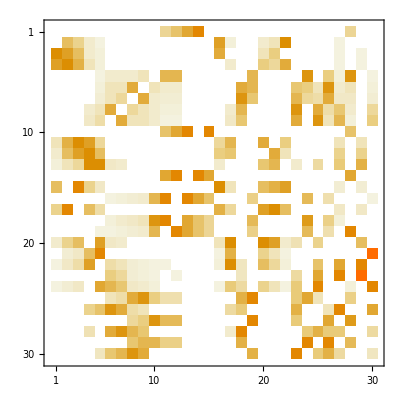

```mathematica
Sort[Graph[Flatten[e],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]//AdjacencyMatrix//Normal//Transpose,Total[#1]<Total[#2]&]//MatrixPlot
```